# Closed-Form Approach to Oscillatory Integrals in Level-Crossing Physics

## Numerical Analysis

Maseim Bassis Kenmoe

University of Dschang

22.06.2025

## I. Modified Parabolic Cylinder Weber functions

### Main functions

```mathematica
(*In this block, we define the Modified Parabolic Cylinder Functions and its complex Conjugate*)

N1:=200; (*Positive integrer. Feel free to adjust this number for our need*)

(*Modified Parabolic Cylinder Weber function*)
ModifiedParabolicCylinderD[k_,ν_,z_]:=Evaluate[Exp[-z^2/4]/Gamma[-ν]∑_(n=0)^N1 ((-z)^n/(n!))2^((n-ν-2)/2)D[Gamma[(n-ν)/2],{ν,k}]]/.{ν->-I ν-1}; 

ModifiedParabolicCylinderDconj[k_,ν_,z_]:=Evaluate[Exp[-z^2/4]/Gamma[-ν]∑_(n=0)^N1 ((-z)^n/(n!))2^((n-ν-2)/2)D[Gamma[(n-ν)/2],{ν,k}]]/.{ν->I ν-1}; (*Conjugate of the Modified Parabolic Cylinder Weber function*)
```

```mathematica
Get["C:\\Users\\HP\\Desktop\\GitHub\\Oscillatory Integrals\\OscillatoryIntegralNumerical.wl"];
```

### Integral_1(τ)

#### Analytical Result

```mathematica
(*-Graphics-*)

F[t_]:=ParabolicCylinderD[-1,-I(1-I)t]Conjugate[ParabolicCylinderD[-1,-I(1-I)t]]/4; (*-Graphics-*)

G[t_]:=π/4 Erf[((1-I) t)/(√2)]+t^2/2 HypergeometricPFQ[{1,1},{3/2,2},ⅈ t^2]
```

#### Numerical Result

```mathematica
L:=100;
sol1=NDSolveValue[{D[y1[t],{t,3}]-1/t D[y1[t],{t,2}]+4 t^2 D[y1[t],t]==-1/t ,y1[-L]==0,y1'[-L]==0,y1''[-L]==1},y1,{t,-L,5},WorkingPrecision->50,PrecisionGoal->30,MaxSteps->Infinity,Method->{"StiffnessSwitching"}];
```

#### Plot

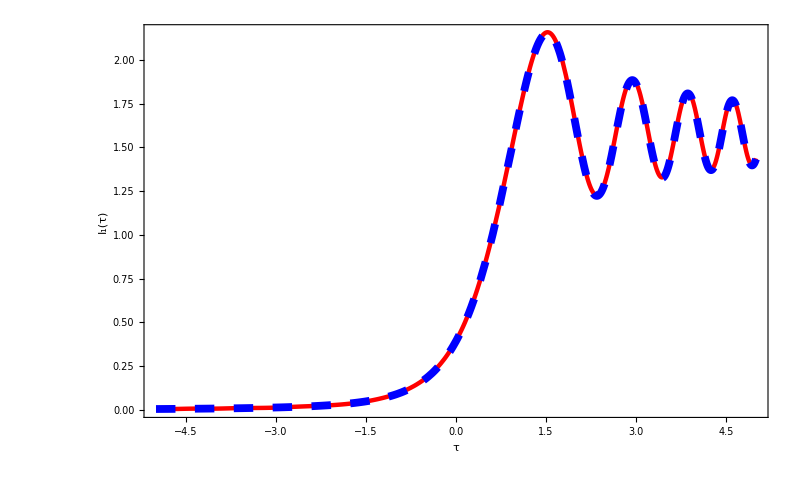

```mathematica
Plot[{sol1[t],Re[G[t]-G[-L]]},{t,-5,5},PlotRange->Automatic,PlotStyle->{{Thickness[0.004], Red},{Thickness[0.007],Dashing[Large],Blue}},Axes->None,Frame->True,FrameLabel->{"τ","I_1(τ)","",""},FrameStyle->Directive[Black,Thick,38,FontFamily->"Times"], ImageSize->800,FrameStyle->{{Black,Black},{Black,Black}}]
```

### Integral_2(τ)

#### Analytical Result

```mathematica
(*-Graphics-*)

(*-Graphics-*)

I2[t_]:=1/64 (4 Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]]+π ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t])/.{ν->0}
```

#### Numerical Result

```mathematica
L=50;

F2[t_?NumericQ]:=Module[{z},z=SetPrecision[-I (1-I) t,30];
(1/4)*Abs[ParabolicCylinderD[-1,z]]^2];

Fprime2[t_?NumericQ]:=(F2[t+10^-5]-F2[t-10^-5])/(2*10^-5);

sys={y1'[t]==y2[t],y2'[t]==y3[t],y3'[t]==(y3[t]-4 t^3 y2[t]+t Fprime2[t]-F2[t])/t};

conds={y1[-L]==0,y2[-L]==0,y3[-L]==F2[-L]};

sol2=NDSolveValue[Join[sys,conds],{y1,y2,y3},{t,-L,5}];
```

#### Plot

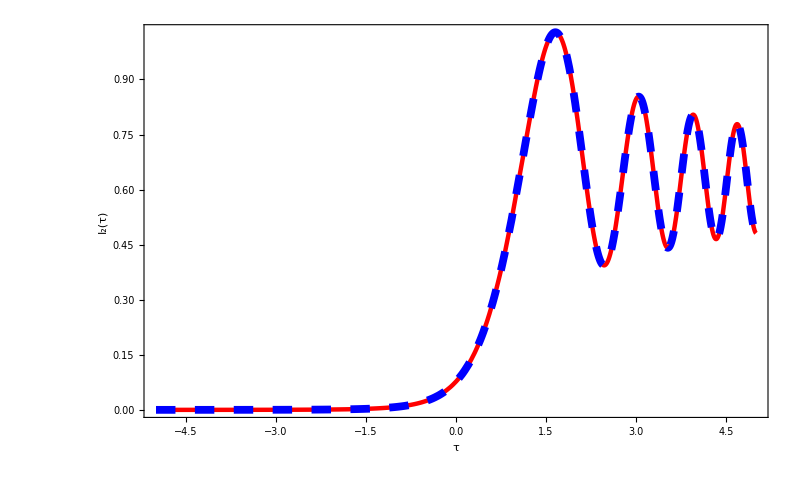

```mathematica
Plot[{sol2[[1]][t],I2[t]},{t,-5,5},PlotRange->Automatic,PlotStyle->{{Thickness[0.004], Red},{Thickness[0.007],Dashing[Large],Blue}},Axes->None,Frame->True,FrameLabel->{"τ","I_2(τ)","",""},FrameStyle->Directive[Black,Thick,38,FontFamily->"Times"], ImageSize->800,FrameStyle->{{Black,Black},{Black,Black}}]
```

### Integral_3(τ)

#### Analytical Result

```mathematica
(*-Graphics-*)

I3[t_]:=1/1536(6 π Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]]+3/4 π^2 ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t]+3 (1/3 π^2 ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t]+2 ModifiedParabolicCylinderD[1,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]-2 Re[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[2,ν,(-1+ⅈ) t]]))/.{ν->0};
```

#### Numerical Result

```mathematica
L=50;

F3[t_?NumericQ]:=sol2[[1]][t]; (*sol2 is calculated from previous section as numerical solution of I_2*)

 Fprime3[t_?NumericQ]:=(F3[t+10^-5]-F3[t-10^-5])/(2*10^-5);

sys3={y1'[t]==y2[t],y2'[t]==y3[t],y3'[t]==(y3[t]-4 t^3 y2[t]+t Fprime3[t]-F3[t])/t};

(*Initial conditions at t=-L*)
conds3={y1[-L]==0,y2[-L]==0,y3[-L]==F3[-L]};

sol3=NDSolveValue[Join[sys3,conds3],{y1,y2,y3},{t,-L,5}];
```

#### Plot

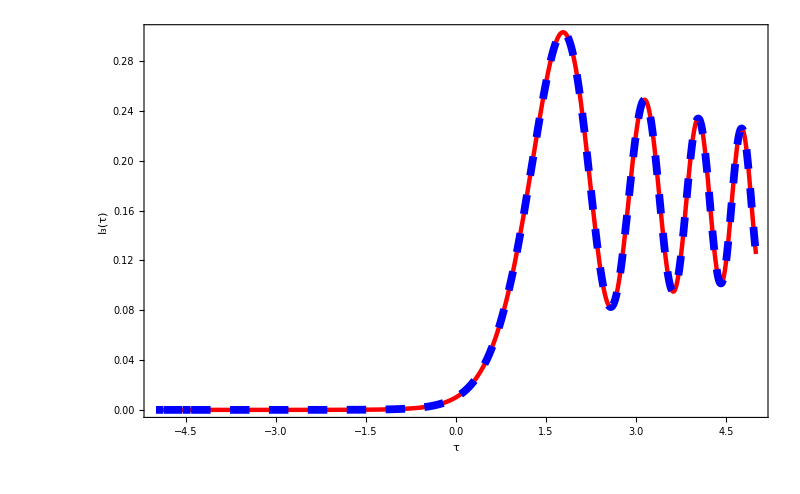

```mathematica
Plot[{sol3[[1]][t],I3[t]},{t,-5,5},PlotRange->Automatic,PlotStyle->{{Thickness[0.004], Red},{Thickness[0.007],Dashing[Large],Blue}},Axes->None,Frame->True,FrameLabel->{"τ","I_3(τ)","",""},FrameStyle->Directive[Black,Thick,38,FontFamily->"Times"], ImageSize->800,FrameStyle->{{Black,Black},{Black,Black}}]
```

### Integral_4(τ)

#### Analytical Result

```mathematica
I4[t_]:=1/49152(6 π^2 Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]]-4 (-2 π^2 Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]]-6 Im[ModifiedParabolicCylinderD[1,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[2,ν,(-1+ⅈ) t]]+2 Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[3,ν,(-1+ⅈ) t]])+1/2 π^3 ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t]+6 π (1/3 π^2 ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t]+2 ModifiedParabolicCylinderD[1,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]-2 Re[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[2,ν,(-1+ⅈ) t]]))/.{ν->0};
```

#### Numerical Result

```mathematica
L:=50;

F4[t_?NumericQ]:=sol3[[1]][t]; (*sol3 is calculated from previous section*)

Fprime4[t_?NumericQ]:=(F4[t+10^-5]-F4[t-10^-5])/(2*10^-5);

sys4={y1'[t]==y2[t],y2'[t]==y3[t],y3'[t]==(y3[t]-4 t^3 y2[t]+t Fprime4[t]-F4[t])/t};

(*Initial conditions at t=-L*)
conds4={y1[-L]==0,y2[-L]==0,y3[-L]==F4[-L]};

sol4=NDSolveValue[Join[sys4,conds4],{y1,y2,y3},{t,-L,5}];
```

#### Plot

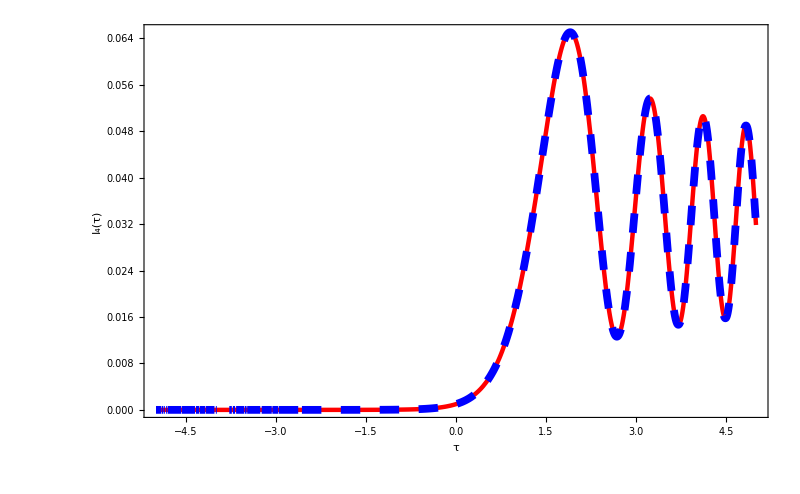

```mathematica
Plot[{sol4[[1]][t],I4[t]},{t,-5,5},PlotRange->Automatic,PlotStyle->{{Thickness[0.004], Red},{Thickness[0.007],Dashing[Large],Blue}},Axes->None,Frame->True,FrameLabel->{"τ","I_4(τ)","",""},FrameStyle->Directive[Black,Thick,38,FontFamily->"Times"], ImageSize->800,FrameStyle->{{Black,Black},{Black,Black}}]
```

### Integral_5(τ)

#### Analytical Result

```mathematica
I5[t_]:=1/1966080(5 π^3 Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]]-10 π (-2 π^2 Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]]-6 Im[ModifiedParabolicCylinderD[1,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[2,ν,(-1+ⅈ) t]]+2 Im[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[3,ν,(-1+ⅈ) t]])+5/16 π^4 ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t]+15/2 π^2 (1/3 π^2 ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t]+2 ModifiedParabolicCylinderD[1,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]-2 Re[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[2,ν,(-1+ⅈ) t]])+5 (1/5 π^4 ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[0,ν,(-1+ⅈ) t]+2 (3 ModifiedParabolicCylinderD[2,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[2,ν,(-1+ⅈ) t]+2 π^2 (ModifiedParabolicCylinderD[1,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[1,ν,(-1+ⅈ) t]-Re[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[2,ν,(-1+ⅈ) t]])-4 Re[ModifiedParabolicCylinderD[1,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[3,ν,(-1+ⅈ) t]]+Re[ModifiedParabolicCylinderD[0,ν,(-1-ⅈ) t] ModifiedParabolicCylinderDconj[4,ν,(-1+ⅈ) t]])))/.{ν->0};
```

#### Numerical Result

```mathematica
L:=50;

F5[t_?NumericQ]:=sol4[[1]][t];

Fprime5[t_?NumericQ]:=(F5[t+10^-5]-F5[t-10^-5])/(2*10^-5);

sys5={y1'[t]==y2[t],y2'[t]==y3[t],y3'[t]==(y3[t]-4 t^3 y2[t]+t Fprime5[t]-F5[t])/t};

(*Initial conditions at t=-L*)
conds5={y1[-L]==0,y2[-L]==0,y3[-L]==F5[-L]};

sol5=NDSolveValue[Join[sys5,conds5],{y1,y2,y3},{t,-L,5}];
```

#### Plot

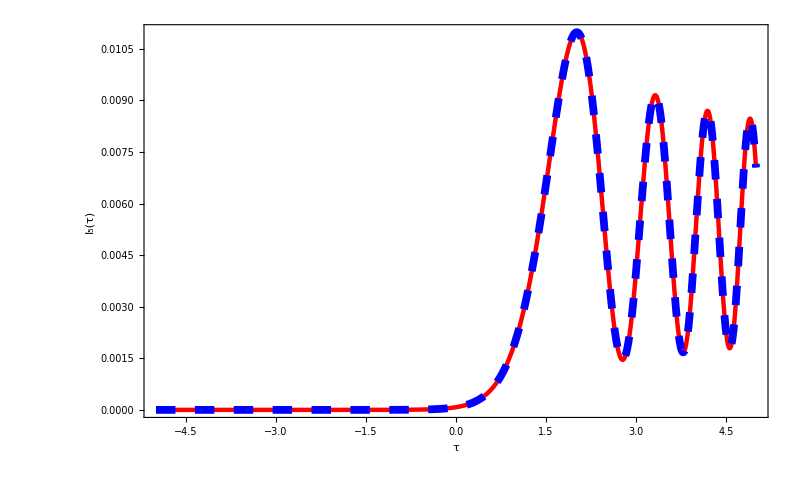

```mathematica
Plot[{sol5[[1]][t],I5[t]},{t,-5,5},PlotRange->Automatic,PlotStyle->{{Thickness[0.004], Red},{Thickness[0.007],Dashing[Large],Blue}},Axes->None,Frame->True,FrameLabel->{"τ","I_5(τ)","",""},FrameStyle->Directive[Black,Thick,38,FontFamily->"Times"], ImageSize->800,FrameStyle->{{Black,Black},{Black,Black}}]
```